To insure reproducibility and to eliminate any question of me cheating or having made a mistake I’m using functions written by Gustafson without any modification.  Specifically all examples here can be repeated by evaluating Gustafson notebook for the defines and then run the example code (and helper definitions) presented here.

My expectation is almost nobody will look at this so I’m only making token efforts of clarity. Naming sucks, minimal comments, etc.

## Common functions defs

### Definitions for manipulating posit and IEEE formats

Posit definations directly from John L. Gustafson’s Mathematica notebook

```mathematica
positQ[p_Integer]:=0≤ p<npat
setpositenv[{n_Integer/;n≥2,e_Integer/;e≥0}]:=
({nbits,es}={n,e};
npat=2^nbits;
useed=2^(2^es);
{minpos,maxpos}={useed^(-nbits+2),useed^(nbits-2)};
qsize=2^⌈Log[2,(nbits-2)2^(es+2)+5]⌉;
qextra=qsize-(nbits-2)2^(es+2);)
twoscomp[sign_,p_]:=Mod[If[sign>0,p,npat-p],npat]
signbit[p_/;positQ[p]]:=IntegerDigits[p,2,nbits]_⟦1⟧
regimebits[p_/;positQ[p]]:=Module[{q=twoscomp[1-signbit[p],p],bits,bit2,npower,tempbits},
bits=IntegerDigits[q,2,nbits];
bit2=bits_⟦2⟧; (* Look for the run length after the sign bit. *)
tempbits=Join[Drop[bits,1],{1-bit2}]; (* Drop the sign bit, but append a complement bit as a sure-fire way to end the run. *)
npower=(Position[tempbits,1-bit2,1,1])_⟦1⟧-1; (* Find first opposite bit. *)
Take[bits,{2,Min[npower+1,nbits]}]]
regimevalue[bits_]:=If[bits_⟦1⟧==1,Length[bits]-1,-Length[bits]]
exponentbits[p_/;positQ[p]]:=Module[{q=twoscomp[1-signbit[p],p],bits,startbit},
startbit=Length[regimebits[q]]+3;
bits=IntegerDigits[q,2,nbits];
If[startbit>nbits,{},Take[bits,{startbit,Min[startbit+es-1,nbits]}]]]
fractionbits[p_/;positQ[p]]:=Module[{q=twoscomp[1-signbit[p],p],bits,startbit},
startbit=Length[regimebits[q]]+3+es;
bits=IntegerDigits[q,2,nbits];
If[startbit>nbits,{},Take[bits,{startbit,nbits}]]]
p2x[p_/;positQ[p]]:=Module[{s=(-1)^signbit[p],k=regimevalue[regimebits[p]],e=exponentbits[p],f=fractionbits[p]},
e=Join[e,Table[0,es-Length[e]]]; (* Pad with 0s on the right if they are clipped off. *)
e=FromDigits[e,2];
If[f=={},f=1,f=1+FromDigits[f,2]×2^(-Length[f])];
Which[
p==0,0,
p==npat/2,ComplexInfinity, (* The two exception values, 0 and ±∞ *)
True,s×useed^k×2^e×f]]
positableQ[x_]:=(Abs[x]==∞∨x∈Reals)
x2p[x_/;positableQ[x]]:=Module[{i,p,e=2^(es-1),y=Abs[x]},
Which[(* First, take care of the two exception values: *)
y==0,0, (* all 0 bits s *)
y==∞,BitShiftLeft[1,nbits-1], (* 1 followed by all 0 bits *)
True,If[y≥1, (* Northeast quadrant: *)
p=1;i=2; (* Shift in 1s from the right and scale down. *)
While[y≥useed∧i<nbits,{p,y,i}={2p+1,y/useed,i+1}]; 
p=2p;i++, (* Else, southeast quadrant: *)
p=0;i=1; (* Shift in 0s from the right and scale up. *)
While[y<1∧i≤nbits,{y,i}={y*useed,i+1}];
If[i≥nbits,p=2;i=nbits+1,p=1;i++]];(* Extract exponent bits: *)
While[e>1/2∧i≤nbits,p=2p;If[y≥2^e,y/=2^e;p++];e/=2;i++];
y--; (* Fraction bits; subtract the hidden bit *)
While[y>0∧i≤nbits,y=2y;p=2p+⌊y⌋;y-=⌊y⌋;i++];
p*=2^(nbits+1-i);i++;(* Round to nearest; tie goes to even *)
i=BitAnd[p,1];p=⌊p/2⌋;
p=Which[
i==0,p, (* closer to lower value *)
y==1∨y==0,p+BitAnd[p,1], (* tie goes to nearest even *)
True,p+1 (* closer to upper value *)];
Mod[If[x<0,npat-p,p],npat (* Simulate 2's complement *)]
] 
]

OverBar[x_]:=p2x[x2p[x]];
SetAttributes[OverBar,Listable]
colorcodep[p_/;positQ[p]]:=Module[{s=signbit[p],r=regimebits[p],e=exponentbits[p],f=fractionbits[p]},
Row[{IntegerString[p,2,nbits],"→", 
Style[If[s==0,"+","-"],RGBColor[1, 0.125, 0]],
Style[Row[r],RGBColor[0.8, 0.6, 0.2]],
If[Length[r]≤nbits-2,Style[1-r_⟦1⟧,RGBColor[0.6, 0.4, 0.2]],""],
If[Length[e]>0,Style[Row[e],RGBColor[0.25, 0.5, 1]],""],
If[Length[f]>0,Row[f],""]}]]
```

#### IEEE style format definitions directly from John L. Gustafson’s Mathematica notebook

```mathematica
setfloatenv[{n_Integer/;n≥4,e_Integer/;e≥2}]:=
({nfbits,esize,fsize}={n,e,n-e-1};
bias=2^(esize-1)-1;
smallsubnormal=2^(1-bias-fsize);
smallnormal=2^(1-bias);
maxfloat=2^bias(1+(2^fsize-1)/2^fsize);
minroundable=smallsubnormal/2;
maxroundable=2^bias(1+(2^fsize-1/2)/2^fsize);)
f2x[f_Integer/;0≤f<2^nfbits]:=Module[{emask=FromDigits[Table[1,esize],2],exp,fmask=FromDigits[Table[1,fsize],2],frac,sgn,smask=BitShiftLeft[1,nfbits-1]},
sgn=BitShiftRight[BitAnd[smask,f],nfbits-1];
exp=BitAnd[BitShiftRight[f,fsize],emask];
frac=BitAnd[fmask,f];
Which[
exp==emask,If[frac==0,(-1)^sgn×∞,Indeterminate],
exp==0,(-1)^sgn×2^(1-bias)×(frac/2^fsize),
True,(-1)^sgn×2^(exp-bias)×(1+frac/2^fsize)]]
floatableQ[x_]:=(x===Indeterminate∨x===∞∨x===-∞∨x∈Reals)
x2f[x_/;floatableQ[x]]:=Module[{e=0,f,sgn,y},
Which[
x===Indeterminate∨¬floatableQ[x],FromDigits[Table[1,nfbits],2], (* NaN exceptions *)
y=Abs[x]; 
sgn=BitShiftLeft[Boole[x<0],nfbits-1];
y==0,0,(* Zero exception *)
y≥maxroundable,BitOr[sgn,BitShiftLeft[FromDigits[Table[1,esize],2],fsize]],(* Infinity and overflow exceptions *)
y<smallnormal,BitOr[sgn,Round[y/smallsubnormal]], (* subnormal exceptions *)
True, (* Else x is normal. Find the exponent and fraction fields. *)
(* At most one of the next two While loops will execute. *)
While[y≥2,y/=2;e++]; 
While[y<1,y*=2;e--]; 
(* We now have 1 ≤ y < 2. *)
f=Round[(y-1)*2^fsize]; (* This may round up to 2, so we add f, instead of ORing it. *)
BitOr[sgn,BitShiftLeft[bias+e,fsize]]+f]]
colorcodef[f_/;floatableQ[f]]:=Module[{fbits=IntegerDigits[f,2,nfbits]},
Row[{ Style[fbits_⟦1⟧,RGBColor[1, 0.125, 0]],"",Style[Row[Take[fbits,{2,esize+1}]],RGBColor[0.25, 0.5, 1]],"",Row[Take[fbits,-nfbits+esize+1]]}]]
UnderBar[x_]:=f2x[x2f[x]]
SetAttributes[UnderBar,Listable]
```

```mathematica
setpositenv[{32,2}]
```

```mathematica
{nbits,es,npat,useed,minpos,maxpos,qsize,qextra}
```

```mathematica
colorcodep[x2p[1.0]]
colorcodep[x2p[-1.0]]
colorcodep[x2p[+1024.0]]
colorcodep[x2p[-1024.0]]
```

```mathematica
fractionbits[x2p[2]]
```

```mathematica
Length[fractionbits[x2p[2]]]
```

```mathematica
ListPlot[Table[Length[fractionbits[x2p[2^i]]],{i,-128,128}], DataRange->{-128,128}]
```

```mathematica
es
```

```mathematica
FullSimplify[2^(2^(i+x))]
```

```mathematica
setpositenv[{32,3}]
bmax=32-(3+es)
{Length[fractionbits[x2p[1]]], bmax-0}
{2^(2^(0+es)),Length[fractionbits[x2p[2^(2^(0+es))]]],bmax-1}
{2^(2^(1+es)),Length[fractionbits[x2p[2^(2^(1+es))]]],bmax-2}
```

```mathematica
Length[fractionbits[x2p[2^208]]]
```

```mathematica
setpositenv[{32,2}];
p2=Table[{i,Length[fractionbits[x2p[2^i]]]},{i,-149,128}];
setpositenv[{32,3}];
p3=Table[{i,Length[fractionbits[x2p[2^i]]]},{i,-220,0}];
```

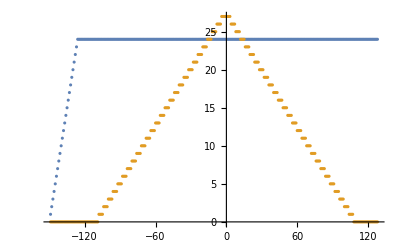

```mathematica
ListPlot[
{Table[{i,If[i>-126,24,Max[24+i+126,0]]},{i,-220,0}],p3
},PlotRange->Full
]
```

```mathematica
ListPlot[Table[Length[fractionbits[x2p[2^i]]],{i,-128,128}]]
```

```mathematica
2^1
```

### Extra derived definitions (by me)

These simply define some basic op over the two number systems.

```mathematica
prnd[x_]:= x̄  (* round input to posit *)
psqrt[x_]:= OverBar[√x]
padd[a_,b_]:= OverBar[a+b]
psub[a_,b_]:= OverBar[a-b]
pmul[a_,b_]:= OverBar[a b]
pdiv[a_,b_]:= OverBar[a/b]
pfma[a_,b_,c_]:= OverBar[(a b)+c]

frnd[x_]:=x̲ (* round input to binary32 *)
fsqrt[x_]:=UnderBar[√x]
fadd[a_,b_]:= UnderBar[a+b]
fsub[a_,b_]:= UnderBar[a-b]
fmul[a_,b_]:= UnderBar[a b]
fdiv[a_,b_]:= UnderBar[a/b]
ffma[a_,b_,c_]:= UnderBar[(a b)+c]

id[x_]:=x

(* the ULP of x for both posit & binary32 *)
pulp[x_]:=p2x[x2p[x]+1]- x̄
fulp[x_]:=f2x[x2f[x]+1]-x̲

(* representable value after x (aka successor) *)
pnext[x_]:=p2x[x2p[x]+1]
fnext[x_]:=f2x[x2f[x]+1]

(* representable value before x (aka predecessor) *)
pprev[x_]:=p2x[x2p[x]-1]
fprev[x_]:=f2x[x2f[x]-1]

(* 
  returns {bits, exp} decimal point implied after first digit:
   {111001,-2} = 1.1001*2^(-2)
 *)
ftobin[Rational[n_,d_]]:= {BaseForm[n,2],-Log2[d]+Floor[Log2[n]]}
ftobin[i_Integer]:= {BaseForm[i,2],Floor[Log2[i]]}

SetAttributes[frnd, {Listable}];
SetAttributes[prnd, {Listable}];
SetAttributes[ftobin, {Listable}];
SetAttributes[id, {Listable}];
```